```mathematica
a=4.35196*10^6;
b=0.030554;
e=1;
H0=a/e*{{0,0,0},{0,b,0},{0,0,1}};
H0//MatrixForm
```

(0. | 0. | 0.
0. | 132970. | 0.
0. | 0. | 4.35196×10^6)

```mathematica
γ=6.5956*10^4;
n=10.54;
u[ξ_]:=γ*ⅇ^(-1*n *ξ)
s12=Sqrt[0.308];
s23=Sqrt[0.437];
s13=Sqrt[0.0234];
c12=Sqrt[1-s12^2];
c23=Sqrt[1-s23^2];
c13=Sqrt[1-s13^2];
W={{c13^2*c12^2,c12*s12*c13^2,c12*c13*s13},{c12*s12*c13^2,s12^2*c13^2,s12*c13*s13},{c12*s13*c13,s12*c13*s13,s13^2}};
W//MatrixForm
```

(0.675807 | 0.450864 | 0.125753
0.450864 | 0.300793 | 0.0838961
0.125753 | 0.0838961 | 0.0234)

```mathematica
DOPRICoeffs[5,p_]:=N[{{{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}},{35/384,0,500/1113,125/192,-2187/6784,11/84,0},{1/5,3/10,4/5,8/9,1,1},{71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40}},p];
```

```mathematica
ψ[ξ_]:={ψ1[ξ],ψ2[ξ],ψ3[ξ]}
```

```mathematica
sol=NDSolve[{ⅈ*D[ψ[ξ],ξ]==(H0+u[ξ]*W).ψ[ξ],ψ[0.1]=={c12 c13,s12 c13, s13}},{ψ1,ψ2,ψ3},{ξ,0.1,1}, Method->{"ExplicitRungeKutta","Coefficients"->DOPRICoeffs,"DifferenceOrder"->5,"StiffnessTest"->False},StartingStepSize->0.25,MaxSteps->Infinity,MaxStepFraction->1/12,WorkingPrecision->MachinePrecision,AccuracyGoal->Infinity];
```

```mathematica
uf[x_]:= Evaluate[{ψ1[ξ],ψ2[ξ],ψ3[ξ]}/.sol]/.{ξ->x}/.{ξ_}->ξ;
```

```mathematica
quf[v_]:=Abs[v[[1]]]^2+Abs[v[[2]]]^2+Abs[v[[3]]]^2;
```

```mathematica
absuf[v_] := {Abs[v[[1]]]^2,Abs[v[[2]]]^2,Abs[v[[3]]]^2};
```

```mathematica
reimuf[v_]:={Re[v[[1]]],Im[v[[1]]],Re[v[[2]]],Im[v[[2]]],Re[v[[3]]],Im[v[[3]]]};
```

```mathematica
surProb[v_]:=c12^2*c13^2*Abs[v[[1]]]^2+s12^2*c13^2*Abs[v[[2]]]^2+s13^2*Abs[v[[3]]]^2;
```

```mathematica
arguf[v_] := {Arg[v[[1]]],Arg[v[[2]]],Arg[v[[3]]]};
st=10^(-5);
```

```mathematica
dat1=Table[Flatten[{x,surProb[uf[x]],reimuf[uf[x]],arguf[uf[x]],absuf[uf[x]],quf[uf[x]]-1}],{x,0.101,0.5,st}];
```

```mathematica
Export["DOPRI_0.00001.dat",dat1,"Table"]
```

DOPRI_0.00001.dat

```mathematica
"DOPRI_0 00001.dat"
```

DOPRI_0 00001.dat

```mathematica
P = c12^2*c13^2*Abs[res[[1]]]^2+s12^2*c13^2*Abs[res[[2]]]^2+s13^2*Abs[res[[3]]]^2
```

Part::partd: Part specification res⟦1⟧ is longer than depth of object.

Part::partd: Part specification res⟦2⟧ is longer than depth of object.

Part::partd: Part specification res⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

0.675807 Abs[res⟦1⟧]^2+0.300793 Abs[res⟦2⟧]^2+0.0234 Abs[res⟦3⟧]^2

```mathematica
q=Abs[res[[1]]]^2+Abs[res[[2]]]^2+Abs[res[[3]]]^2
```

Part::partd: Part specification res⟦1⟧ is longer than depth of object.

Part::partd: Part specification res⟦2⟧ is longer than depth of object.

Part::partd: Part specification res⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Abs[res⟦1⟧]^2+Abs[res⟦2⟧]^2+Abs[res⟦3⟧]^2

```mathematica
q-1
```

-1+Abs[res⟦1⟧]^2+Abs[res⟦2⟧]^2+Abs[res⟦3⟧]^2

```mathematica
x0=0.5;
```

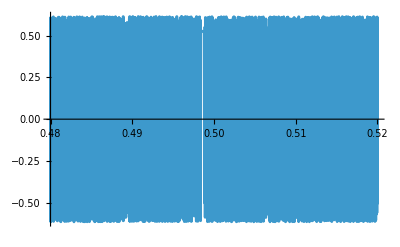

```mathematica
dx=0.04;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[Re[uf[x][[2]]],{x,x1,x2}]
```

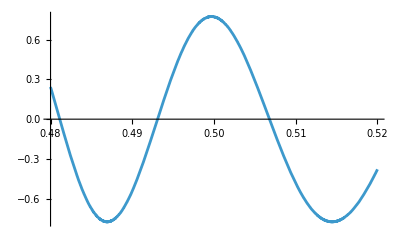

```mathematica
dx=0.04;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[Im[uf[x][[1]]],{x,x1,x2}]
```

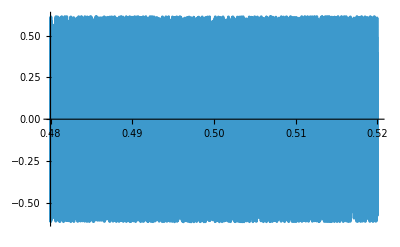

```mathematica
dx=0.04;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[Im[uf[x][[2]]],{x,x1,x2}]
```

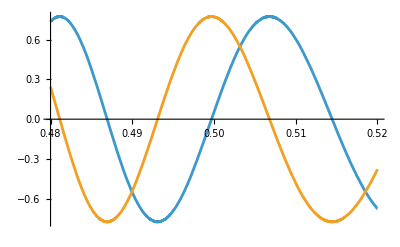

```mathematica
dx=0.04;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[{Re[uf[x][[1]]],Im[uf[x][[1]]]},{x,x1,x2}]
```

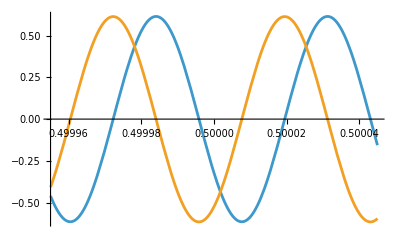

```mathematica
dx=0.00009;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[{Re[uf[x][[2]]],Im[uf[x][[2]]]},{x,x1,x2}]
```

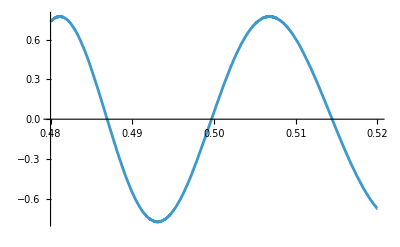

```mathematica
dx=0.04;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[Re[uf[x][[1]]],{x,x1,x2}]
```

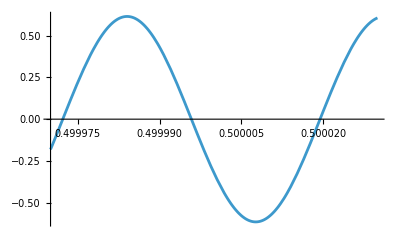

```mathematica
dx=0.00006;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[Re[uf[x][[2]]],{x,x1,x2}]
```

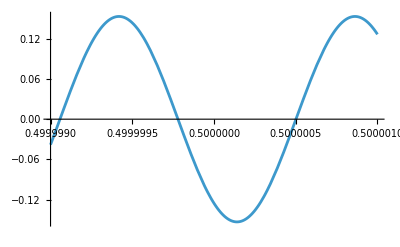

```mathematica
dx=0.000002;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[Re[uf[x][[3]]],{x,x1,x2}]
```

```mathematica
dx=0.04;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[Im[uf[x][[1]]],{x,x1,x2}]
```

-Graphics-

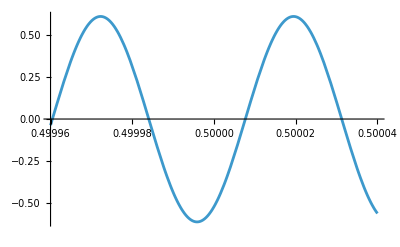

```mathematica
dx=0.00008;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[Im[uf[x][[2]]],{x,x1,x2}]
```

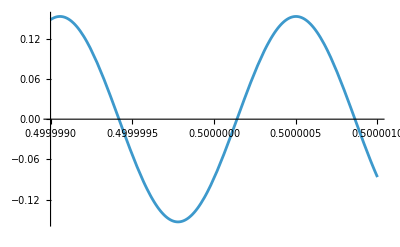

```mathematica
dx=0.000002;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[Im[uf[x][[3]]],{x,x1,x2}]
```

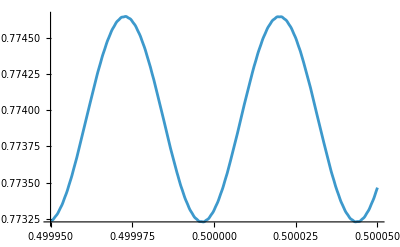

```mathematica
dx=0.0001;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[Abs[uf[x][[1]]],{x,x1,x2}]
```

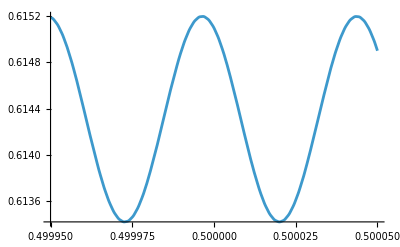

```mathematica
dx=0.0001;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[Abs[uf[x][[2]]],{x,x1,x2}]
```

```mathematica
dx=0.0001;
x1=x0-0.5*dx;
x2=x0+0.5*dx;
Plot[Abs[uf[x][[3]]],{x,x1,x2}]
```

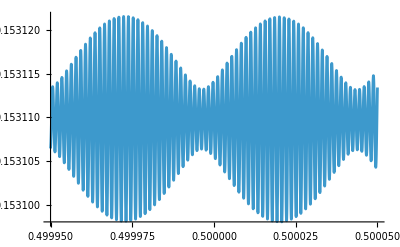

-Graphics-